# Standard Deviation

```mathematica
SetDirectory[NotebookDirectory[]];
MatGenQ0[n_]:=Table[If[Mod[j+k,2]==0,1/(1-(j-k)^2),0],{j,0,n-1},{k,0,n-1}];
MatGenQy[n_,y_]:=Table[If[Mod[j+k,2]==0,(3-(j-k)^2)/(4(1-(j-k)^2)(9-(j-k)^2))+(y-0.5)^2/(1-(j-k)^2),(-(y-0.5))/(4-(j-k)^2)],{j,0,n-1},{k,0,n-1}];
```

#### Lower Bound

```mathematica
Ls={64,256,1024};
ys=Range[0.01,0.99,0.01];
dataRy=Table[L^2/Eigenvalues[N@{MatGenQ0[L],MatGenQy[L,y]},1][[1]],{L,Ls},{y,ys}];
```

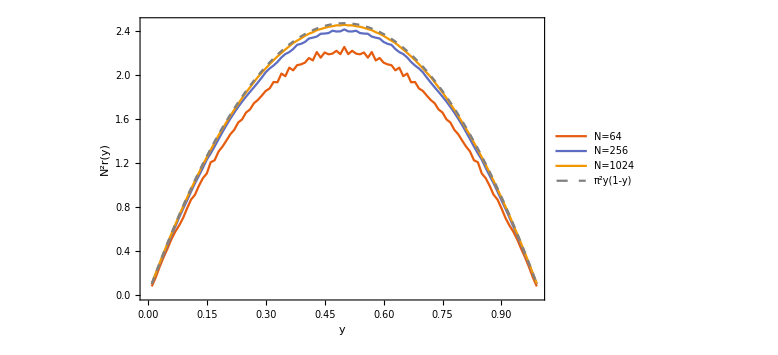

```mathematica
plotRy=ListLinePlot[Join[Map[Transpose[{Range[0.01,0.99,0.01],#}]&,dataRy],
{Table[{y,Pi^2 y(1-y)},{y,ys}]}],
PlotLegends->Placed[
PointLegend[Join[Table[StringForm["N=`1`",L],{L,Ls}],{"π^2y(1-y)"}],
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLayout->{"Column",2}],
Scaled[{0.5,0.2}]],
PlotStyle->Join[Table[Automatic,Length[Ls]],{{Gray,Dashed}}],
LabelStyle->Directive[FontSize->20,FontFamily->"Times",Black],
ImageSize->Large,
Frame->True,
FrameLabel->{{"N^2r(y)",None},{"y",None}},FrameStyle->Directive[FontSize->20,FontFamily->"Times"],PlotStyle->Thick,PlotTheme->"Scientific",
GridLines->{{0,1},{0,Pi^2/4}}
]
```

```mathematica
Export["ry.pdf",plotRy]
```

ry.pdf

#### Comparison with selected polynomials

```mathematica
Ls=2^Range[3,12];
std=Table[Sqrt@Sum[
Module[{ak,bk,coeffs,intp,intp1,intp2},
ak=N@Table[Sin[Pi (l+1)/(L+1)],{l,0,L-1}];
bk=ListConvolve[Reverse[ak],Join[ak,Table[0,{L-1}]]];
coeffs=N@Join[{1/L},Table[4/(L(L+1))Cos[(2Pi m k)/L]bk[[m+1]],{m,1,L-1}]];
{intp,intp2}=Sum[{1/(1-m^2),(3-m^2)/(4(1-m^2)(9-m^2))}coeffs[[m+1]],{m,0,L-1,2}];
intp1=Sum[1/(2(4-m^2))coeffs[[m+1]],{m,1,L-1,2}];
intp2-intp1^2/intp
],{k,0,L-1}]*L,
{L,Ls}
]
```

{1.03196,1.164,1.22699,1.25602,1.26964,1.27619,1.27939,1.28098,1.28177,1.28216}

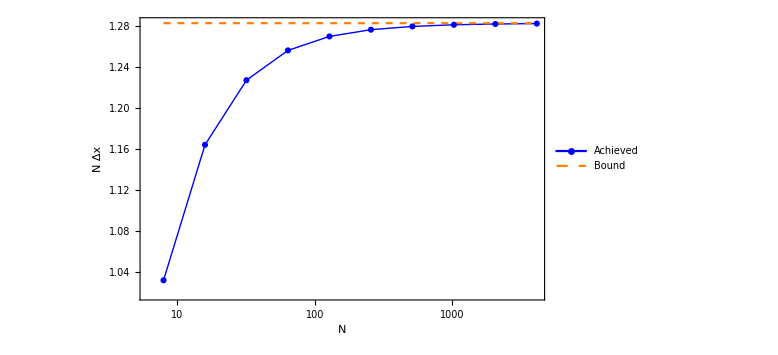

```mathematica
plotStd=ListLogLinearPlot[
Map[
Transpose[{Ls,#}]&,
{std,Table[Pi/Sqrt[6],Length[Ls]]}
],
Joined->True,
PlotLegends->Placed[
PointLegend[{"Achieved","Bound"},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLayout->{"Column",1}],
Scaled[{0.8,0.2}]],
PlotStyle->{{Thick,Blue},{Orange,Dashed}},
PlotMarkers->{Automatic,None},
MeshStyle->Automatic,
LabelStyle->Directive[FontSize->20,FontFamily->"Times",Black],
ImageSize->Large,
Frame->True,
FrameLabel->{{"N Δx",None},{"N",None}},FrameStyle->Directive[FontSize->20,FontFamily->"Times"],PlotStyle->Thick,PlotTheme->"Scientific",
PlotRange->Full
]
```

```mathematica
Export["std.pdf",plotStd]
```

std.pdf